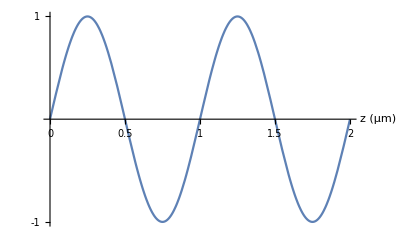

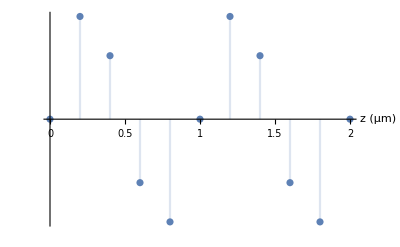

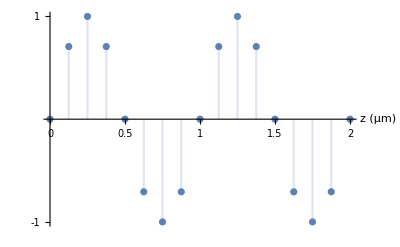

```mathematica
Plot[Sin[2π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"z (μm)", None},AxesStyle->Directive["Label", 16]]
DiscretePlot[Sin[2π t],{t,0,2,0.2},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"z (μm)", None},AxesStyle->Directive["Label", 16]]
DiscretePlot[Sin[2π t],{t,0,2,0.125},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"z (μm)", None},AxesStyle->Directive["Label", 16]]
```

```mathematica
UnitConvert[5*(1.μm)/c,fs]
```

16.6782 fs

```mathematica
UnitConvert[0.5/10*(0.3μm)/c,fs]
```

0.0500346 fs

```mathematica
0.5/16.
```

0.03125

```mathematica
5/0.03125
```

160.

```mathematica
1/16.
```

0.0625

```mathematica
1.4^2
```

1.96

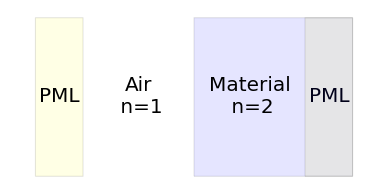

```mathematica
Graphics[{Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Rectangle[{0,0},{3,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1]},Yellow],
Style[Rectangle[{17,0},{20,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1],Yellow}],
Rotate[Text[Style["PML",FontSize->20],{1.5,5}],90°],
Rotate[Text[Style["PML",FontSize->20],{18.5,5}],90°],
Style[Rectangle[{3,0},{10,10}],{EdgeForm[{Dashed, Black}],Opacity[0],White}],
Style[Rectangle[{10,0},{20,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1],Blue}],
Text[Style["Air\n n=1",FontSize->20],{6.5,5}],
Text[Style["Material\n n=2",FontSize->20],{13.5,5}]
}]
```

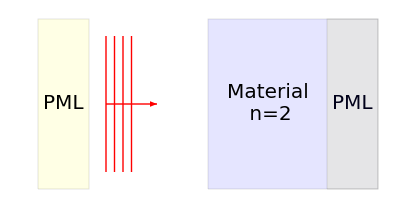

```mathematica
Graphics[{
Style[Line[{{5,1},{5,9}}],Red],
Style[Line[{{4.5,1},{4.5,9}}],Red],
Style[Line[{{4,1},{4,9}}],Red],
Style[Line[{{5.5,1},{5.5,9}}],Red],
Style[Arrow[{{4,5},{7,5}}],Red,Thick],
Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Rectangle[{0,0},{3,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1]},Yellow],
Style[Rectangle[{17,0},{20,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1],Yellow}],
Rotate[Text[Style["PML",FontSize->20],{1.5,5}],90°],
Rotate[Text[Style["PML",FontSize->20],{18.5,5}],90°],
Style[Rectangle[{3,0},{10,10}],{EdgeForm[{Dashed, Black}],Opacity[0],White}],
Style[Rectangle[{10,0},{20,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1],Blue}],
Text[Style["Material\n n=2",FontSize->20],{13.5,5}]
}]
```

```mathematica
0.667*0.5
```

0.3335

```mathematica
1/3+0.5
```

0.833333

```mathematica
((1-2)/(1+2))^2
```

1/9

```mathematica
8./9
```

0.888889

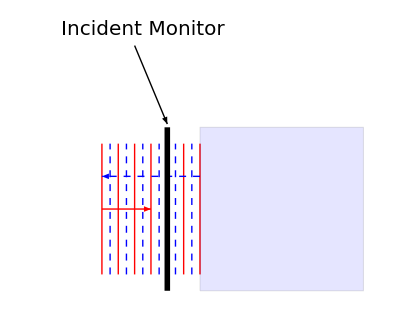

```mathematica
Graphics[{
Table[Style[Line[{{n,1},{n,9}}],Red],{n,4.,10,1}],
Table[Style[Line[{{n,1},{n,9}}],Blue,Dashed],{n,4.5,10,1}],
Style[Arrow[{{4,5},{7,5}}],Red,Thick],
Style[Arrow[{{10,7},{4,7}}],Blue,Dashed],
Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Rectangle[{10,0},{20,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1],Blue}],
Style[Line[{{8,0},{8,10}}],Thickness[0.01]],
Arrow[{{6,15},{8,10.2}}],
Text[Style["Incident Monitor",FontSize->20],{6.5,16}]
}]
```

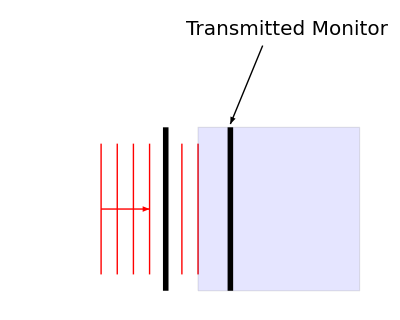

```mathematica
Graphics[{
Table[Style[Line[{{n,1},{n,9}}],Red],{n,4.,10,1}],
Style[Arrow[{{4,5},{7,5}}],Red,Thick],
Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Rectangle[{10,0},{20,10}],{EdgeForm[{Dashed, Black}],Opacity[0.1],Blue}],
Style[Line[{{12,0},{12,10}}],Thickness[0.01]],
Arrow[{{14,15},{12,10.2}}],
Text[Style["Transmitted Monitor",FontSize->20],{15.5,16}],
}]
```